# CCBH-Direct: k x minMass exclusion plots (newData)

Davi  C. Rodrigues (this code). October, 2023.

```mathematica
ResourceFunction["DarkMode"][]
```

CCBH = Cosmologically coupled black hole (general case)
DEBH = Dark energy coupled Black Hole (implies k = - 3w)
GBH = Growing BH, k is arbitrary and without direct dark energy impact.
m1 = primary (larger) mass of the BBH or NSBH pair.

Naming conventions:
All defined variables/functions start with lower case letter.
“I” at the end of a function name: interpolated version. 
“Raw”: a function without options. It is useful to store results. The version with options is based on the raw version.

## Starting...

```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{"codes", "Directories.wl"}]];

(*
  Calling wl files
  ***************** 
*)

getCode["Constants.wl"];
baseSimPoints = 10^4; (*The base number of points to be simmulated for each dimension. For this notebook, this is a good value since this value will be multiplied by 72*)

getCode["ObsDataPreparationGWTC-3.wl"]; 
(*getCode["PowerLawPlusPeakDefinition.wl"];*)
getCode["Cosmology.wl"];
(*getCode["MassFactorCorrection.wl"];*)

Print["End of running wl files."];

(*
  GENERAL PURPOSE FUNCTIONS
  **************************
*)

(*Better names: probSigma[nSigma_] and sigmaProb[prob_]*)

sigmaProb::usage = "sigmaProb[probability] yields the number of σ's for a given probability.";
sigmaProb[prob_] := Block[{sigma}, 
  sigma /. FindRoot[NProbability[RealAbs[x] > sigma , x\[Distributed]NormalDistribution[]] == prob, {sigma, 0, 10}]
];

Clear[probSigma];
probSigma[n_] := probSigma[n] = NProbability[RealAbs[x] > n, x\[Distributed]NormalDistribution[]];

SetSystemOptions["ParallelOptions" -> {"ParallelThreadNumber" -> 1, "MKLThreadNumber"->1}]
```

Starting Constants.wl:

Starting ObsDataPreparationGWTC-3.wl:

Number of m1 black holes:   72

Starting Cosmology.wl:

tableZformation loaded.

End of running wl files.

ParallelOptions→{AbortPause→2.,BusyWait→0.01,MathLinkTimeout→15.,MKLThreadNumber→1,ParallelThreadNumber→1,RecoveryMode→ReQueue,RelaunchFailedKernels→False,VectorParallelLengthThresholds→{32768,8192,8192,8192},VectorVendorLengthThresholds→{128,32,32}}

## Exclusion plot k x MinMass using random Direct method mass values

### General

Some definitions below focus on the current data, but these will be redefined for the forecast. 
Other definitions and data are important for the forecasts as well.

```mathematica
(*
  Geting and preparing the data 
  ------------------------------
*)

(* 
  OLD APPROACH
  eventsFileNames = FileNames["*.txt", FileNameJoin[{pathIn, "lvk_posteriors"}]];
  posteriorM1event[event_] :=  posteriorM1event[event] = Import[
    eventsFileNames[[event]], "Table"
]   // Take[#, 4001] & // Drop[#, 1] & // Part[#, All, {6, 3}] & ; (*Picks redshift and sourcemass*)
*)

getIn["LVKzm1m2All.mx"];
Echo[Names["LVK`*"], "Imported context: LVK`. Imported expressions: "];

Clear[posteriorM1event, dataM1];

posteriorM1event[event_] :=  LVK`zm1m2[event][[All, {"redshift", "mass_1_source"}]] // Values;
dataM1aux[i_] :=  posteriorM1event[#][[i]] & /@ Range @ 72; (*takes the i-th data from each event*)
dataM1[i_] := dataM1[i] = {Round[#1, 0.02], #2} & @@@ dataM1aux[i]; (*This Round has sufficient precision and improves speed, due to dataMassFactor1 memory*)
Echo[maxi = Length@posteriorM1event[#] &/@ Range[72] // Min, "max i value that all the vents share: "]; // EchoTiming
(*
  Setting the functions zTime and timeZ:
  ---------------------------------------
*)

(*zTime[t_?NumberQ] := zTime[t, -1];*)
(*table`zTime = ParallelTable[
    {t, zTime[t]}, 
    {t, 0.0005 (*z ~ 1000*), 15, 0.0005}
  ]; // EchoTiming  (*413 seconds*) 
*)
(*dumpsave["tablezTime.mx", table`zTime]*)
getAux["tablezTime.mx"];

table`timeZ = {#2, #1} & @@@ table`zTime; (*It will be used to define the inverse function.*)
zTimeI = Interpolation[table`zTime];
timeZI = Interpolation[table`timeZ]; (*inverse of zTimeI*)

(*
  Setting the delay time distribution
  ------------------------------------
*)

Clear[
  minDelayTime,
  maxDelayTime,
  randomLogDelayTime,
  dataDelayTime
];

minDelayTime = tdmin0; (*min delay time to be computed. In this notebook, there is no need to consider td values smaller than tdmin0*)
maxDelayTime[zObs_, tdmax_?NumberQ, zMax_?NumberQ, w_] := maxDelayTime[zObs, tdmax, zMax, w] = Min[
  tdmax,
  timeZ[zObs, zMax, w] (*timeZ is NOT the same thing as timeZI*)
]; 

randomLogDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_, realizations_] := 
 RandomReal[{Log10[tdmin], Log10 @ maxDelayTime[zObs, tdmax, zMax, w]}, realizations]; (*log-flat distribution.*)

dataDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_] := 10^randomLogDelayTime[zObs, tdmin, tdmax, zMax, w,  baseSimPoints]; 

dataDelayTime[zm_] := dataDelayTime[zm, tdmin0, tdmax0, zMax0, w0];

(*
  Defining the mass factor
  ------------------------
*)

Clear[
  massFactor1, 
  massFactorDelay1, 
  dataMassFactor1, 
  dataM1ObsFormation
];

massFactor1[zm_,zi_] = (1 + zi)/(1 + zm); (*This is the massFactor for k = 1*)

SetAttributes[massFactorDelay1, Listable];
massFactorDelay1[zm_, td_] =  massFactor1[zm, zTimeI[timeZI[zm] - td]];
dataMassFactor1[zm_] := dataMassFactor1[zm] = massFactorDelay1[zm, dataDelayTime[zm]]; (*Rounded values of zm are helpful*)
dataM1ObsFormation[k_, i_] :=  (#2 / dataMassFactor1[#1]^k) &  @@@ dataM1[i];  (*Ideal, but slower and gives the same answer*)
(*dataM1ObsFormation[k_, i_] := (# / dataMassFactor1[0.4]^k) & /@  dataM1[i][[All, 2]];*) (*All the redshifts are taken to be 0.4, approximation*)

dataM1[3]; // EchoTiming
```

Imported context: LVK`. Imported expressions:   {LVK`file,LVK`zm1m2}

max i value that all the vents share:   1993

3.65635

3.62187

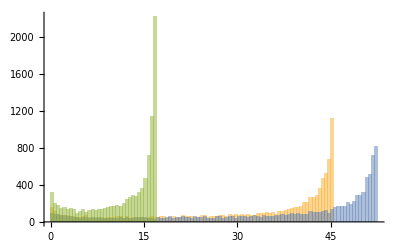

```mathematica
Histogram[dataM1ObsFormation[3,1][[{10, 20 ,30}]], {0.5}]
```

### Current data

```mathematica
(*Clear[𝒟M1ObsFormation];
𝒟M1ObsFormation[k_, event_, i_] := EmpiricalDistribution[dataM1ObsFormation[k, i][[event]]];*)
Clear[𝒟M1ObsFormation];
𝒟M1ObsFormation[k_, i_] :=  EmpiricalDistribution /@ dataM1ObsFormation[k, i];
```

```mathematica
𝒟M1ObsFormation[2.7, 77]; // EchoTiming
```

4.15848

```mathematica
Clear[probabiltyNoBHwithMassBelow];
(*probabiltyNoBHwithMassBelow[k_, minM_, i_] := Product[SurvivalFunction[𝒟M1ObsFormation[k, event, i], minM], {event, 1, 72}];*)
probabiltyNoBHwithMassBelow[k_, minM_, i_] := Times @@ (SurvivalFunction[#, minM] & /@ 𝒟M1ObsFormation[k, i]);
```

```mathematica
probabiltyNoBHwithMassBelow[1, 2, 1] // EchoTiming
probabiltyNoBHwithMassBelow[2, 2, 1] // EchoTiming
probabiltyNoBHwithMassBelow[3, 2, 1] // EchoTiming
probabiltyNoBHwithMassBelow[1, 2, 2] // EchoTiming
probabiltyNoBHwithMassBelow[2, 2, 2] // EchoTiming
probabiltyNoBHwithMassBelow[3, 2, 2] // EchoTiming
```

0.178536

0.814693

0.179263

0.126995

0.181297

0.00832957

3.89596

0.809775

0.189067

0.136114

0.187601

0.00946425

```mathematica
Clear[tab, sol, solAll];

probValue = probSigma[2];
listk1 = Range[0.5, 3, 0.1];
listm1 = Range[0.9, 5.0, 0.1]; (*For the Forecast, minimmal mass = 0.9 and maximum 5.0.*)
sol[0, i_] = {arbitraryK, Last @ listm1}; (*Only used for the first step.*)

tab[nk1_, i_] := tab[nk1, i] = Block[{nm1Previous, nm1Minimal, listm1Relevant},
  nm1Previous = Position[listm1, Last @ sol[nk1-1, i]][[1,1]];
  nm1Minimal = If[nm1Previous - 7 < 1, 1, nm1Previous - 7]; 
  listm1Relevant = listm1 // Take[#, {nm1Minimal, nm1Previous}] &;
  Table[
    {{listk1[[nk1]], m1}, Abs[probabiltyNoBHwithMassBelow[listk1[[nk1]], m1, i] - probValue]} , 
    {m1, listm1Relevant}
  ]
];
sol[nk1_, i_] := sol[nk1, i] = tab[nk1, i] // SortBy[#, Last][[1,1]] & (*// Echo*);

solAll[i_] := solAll[i] = Monitor[Table[sol[nk1, i], {nk1, Length @ listk1}], nk1];
```

```mathematica
tab[1,1] // EchoTiming
```

1.45803

{{{0.5,4.3},0.747712},{{0.5,4.4},0.725746},{{0.5,4.5},0.702773},{{0.5,4.6},0.675245},{{0.5,4.7},0.645368},{{0.5,4.8},0.614717},{{0.5,4.9},0.580699},{{0.5,5.},0.543799}}

```mathematica
(*table300DirectZM = Monitor[Table[solAll[i], {i, 1, 300}], i];*)
(*dumpsave["table300DirectZM.mx", table300DirectZM];*)
getAux["table300DirectZM.mx"];
```

### Forecast with 250 events

```mathematica
nForecast = 250;
Clear[dataForecastAll, dataForecast];
dataForecastAll = Join@@(dataM1[#][[All, 2]] & /@  Range[1000]);
dataForecast[i_]:= dataForecast[i] = Take[RandomSample @ dataForecastAll, nForecast];
```

$Aborted

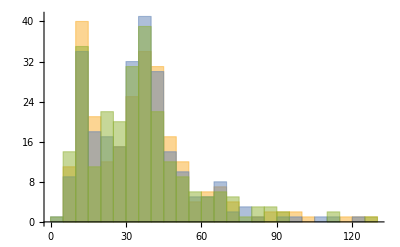

```mathematica
Histogram[{dataForecast[1], dataForecast[2], dataForecast[3]}, {5}]
```

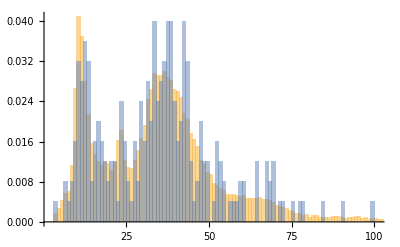

```mathematica
Histogram[{dataForecastAll, dataForecast[2]}, {1}, "PDF"]
```

```mathematica
Clear[𝒟M1ObsFormationF, 𝒟M1ObsFormationF, dataMassFactor1, probabiltyNoBHwithMassBelowF];

baseSimPoints = 5 10^3; 
(*Due to the ``small'' baseSimPoints, there is a relevant variation in the probability of a given realization, 
but it is compensated by 250 events being evaluated with several i values, and then picking the 5% quantile*)
dataMassFactor1[zm_] := dataMassFactor1[zm] = massFactorDelay1[zm, dataDelayTime[zm]]

dataM1ObsFormationF[k_, i_] :=  (# /dataMassFactor1[0.4]^k) & /@ dataForecast[i];

𝒟M1ObsFormationF[k_, i_] := EmpiricalDistribution /@ dataM1ObsFormationF[k, i];

probabiltyNoBHwithMassBelowF[k_, minM_, i_] := Times @@ (SurvivalFunction[#, minM] & /@ 𝒟M1ObsFormationF[k, i]);
```

Some of the masses in this approach can be < 5 Msun. See examples below. It’s about 1 case in each of the 250 cases. Clearly, this is less relevant for the 72 sample case. If there is a BH with mass < 5 Msun,  the probability of having no BH with mass < 5 BH goes to zero. This issue is only relevant for

```mathematica
N[Sort[dataForecast[1]][[1;;5]], 3]
N[Sort[dataForecast[2]][[1;;5]], 3]
N[Sort[dataForecast[3]][[1;;5]], 3]
N[Sort[dataForecast[4]][[1;;5]], 3]
N[Sort[dataForecast[5]][[1;;5]], 3]
```

{5.92,6.73,6.95,7.16,7.43}

{3.25,6.28,6.43,7.07,8.14}

{4.78,5.78,6.02,6.8,7.37}

{4.86,5.31,5.4,5.66,5.89}

{3.85,4.6,5.64,8.19,9.24}

```mathematica
probabiltyNoBHwithMassBelowF[2, 2, 4] 
probabiltyNoBHwithMassBelowF[2, 2, 5] 
probabiltyNoBHwithMassBelowF[2, 2, 6]
```

0.000458338

0.00086247

0.000597063

```mathematica
probabiltyNoBHwithMassBelowF[3, 2, 1] // sigmaProb
probabiltyNoBHwithMassBelowF[3, 2, 2] // sigmaProb
probabiltyNoBHwithMassBelowF[3, 2, 3] // sigmaProb
```

5.55724

5.52173

5.56459

```mathematica
Clear[tabF, solF, solAllF];

probValue = probSigma[2];
listk1 = Range[0.5, 3, 0.1];
listm1 = Range[0.1, 5.0, 0.1]; (*For the Forecast, minimmal mass = 0.1 and maximum 5.0.*)
solF[0, i_] = {arbitraryK, Last @ listm1}; (*Only used for the first step.*)

tabF[nk1_, i_] := tabF[nk1, i] = Block[{nm1Previous, nm1Minimal, listm1Relevant},
  nm1Previous = Position[listm1, Last @ solF[nk1-1, i]][[1,1]];
  nm1Minimal = If[nm1Previous - 10 < 1, 1, nm1Previous - 10]; 
  listm1Relevant = listm1 // Take[#, {nm1Minimal, nm1Previous}] &;
  Table[
    {{listk1[[nk1]], m1}, Abs[probabiltyNoBHwithMassBelowF[listk1[[nk1]], m1, i] - probValue]} , 
    {m1, listm1Relevant}
  ]
];
solF[nk1_, i_] := solF[nk1, i] = tabF[nk1, i] // SortBy[#, Last][[1,1]] & (*// Echo*);

solAllF[i_] := solAllF[i] = Monitor[Table[solF[nk1, i], {nk1, Length @ listk1}], nk1];
```

```mathematica
tabF[1,1]
```

{{{0.5,4.},0.0455003},{{0.5,4.1},0.0455003},{{0.5,4.2},0.0455003},{{0.5,4.3},0.0455003},{{0.5,4.4},0.0455003},{{0.5,4.5},0.0455003},{{0.5,4.6},0.0455003},{{0.5,4.7},0.0455003},{{0.5,4.8},0.0455003},{{0.5,4.9},0.0455003},{{0.5,5.},0.0455003}}

```mathematica
(*table300DirectF = Table[solAllF[i], {i, 1, 300}];*)
(*dumpsave["table300DirectF.mx", table300DirectF];*)
(*exportAux["table300DirectF.json", table300DirectF]*)
getAux["table300DirectF.mx"];
```

### Forecast with all data together

For some reason, loading dataM1 with the new data is much slower than with the old one. The development below, apart from the histogram was

```mathematica
288000 / 72.
```

4000.

```mathematica
dataForecast = Join@@(dataM1[#][[All, 2]] & /@  Range[500]); (*i.e., data to be used for this forecast*)
```

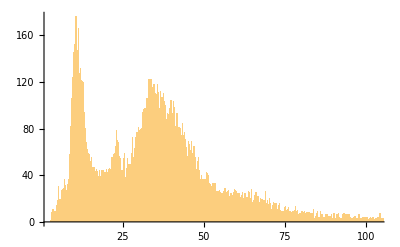

```mathematica
Histogram[dataForecast, {0.1}]
```

```mathematica
Clear[𝒟M1ObsFormationF, 𝒟M1ObsFormationF];

Clear[dataMassFactor1]
baseSimPoints =  Length @ dataForecast;
dataMassFactor1[zm_] := dataMassFactor1[zm] = massFactorDelay1[zm, dataDelayTime[zm]];

dataM1ObsFormationF[k_] :=  dataForecast / dataMassFactor1[0.4]^k; 
(*dataM1ObsFormationF[k_] :=  Flatten[(# / dataMassFactor1[0.4]^k )& /@ dataForecast];*)

𝒟M1ObsFormationF[k_] := 𝒟M1ObsFormationF[k] =  EmpiricalDistribution[dataM1ObsFormationF[k]];
```

```mathematica
dataM1ObsFormationF[3]// Length
```

288000

```mathematica
𝒟M1ObsFormationF[3]; // EchoTiming
```

0.247204

```mathematica
CDF[𝒟M1ObsFormationF[3], 2]
```

0.0630451

```mathematica
Clear[probabiltyNoBHwithMassBelowF];
(*probabiltyNoBHwithMassBelow[k_, minM_, i_] := Product[SurvivalFunction[𝒟M1ObsFormation[k, event, i], minM], {event, 1, 72}];*)
probabiltyNoBHwithMassBelowF[k_, minM_] := SurvivalFunction[𝒟M1ObsFormationF[k], minM]^250;
```

```mathematica
probabiltyNoBHwithMassBelowF[3, 2] // sigmaProb
```

5.35608

```mathematica
Clear[tabF, solF, solAllF];

probValue = probSigma[2];
listk1 = Range[0.5, 3, 0.1];
listm1 = Range[0.1, 5.0, 0.1]; (*For the Forecast, minimmal mass = 0.1 and maximum 5.0.*)
solF[0] = {arbitraryK, Last @ listm1}; (*Only used for the first step.*)

tabF[nk1_] := tabF[nk1] = Block[{nm1Previous, nm1Minimal, listm1Relevant},
  nm1Previous = Position[listm1, Last @ solF[nk1-1]][[1,1]];
  nm1Minimal = If[nm1Previous - 10 < 1, 1, nm1Previous - 10]; 
  listm1Relevant = listm1 // Take[#, {nm1Minimal, nm1Previous}] &;
  Table[
    {{listk1[[nk1]], m1}, Abs[probabiltyNoBHwithMassBelowF[listk1[[nk1]], m1] - probValue]} , 
    {m1, listm1Relevant}
  ]
];
solF[nk1_] := solF[nk1] = tabF[nk1] // SortBy[#, Last][[1,1]] & (*// Echo*);

solAllF := solAllF = Monitor[Table[solF[nk1], {nk1, Length @ listk1}], nk1];
```

```mathematica
tabF[1]
```

{{{0.5,4.},0.345757},{{0.5,4.1},0.316242},{{0.5,4.2},0.282021},{{0.5,4.3},0.24717},{{0.5,4.4},0.214195},{{0.5,4.5},0.183118},{{0.5,4.6},0.15522},{{0.5,4.7},0.127208},{{0.5,4.8},0.103351},{{0.5,4.9},0.0860758},{{0.5,5.},0.066403}}

```mathematica
table300DirectFAll = solAllF // EchoTiming
dumpsave["table300DirectFAll.mx", table300DirectFAll]
```

0.

{{0.5,5.},{0.6,5.},{0.7,4.8},{0.8,4.5},{0.9,4.1},{1.,3.8},{1.1,3.5},{1.2,3.1},{1.3,2.8},{1.4,2.5},{1.5,2.2},{1.6,1.9},{1.7,1.7},{1.8,1.5},{1.9,1.3},{2.,1.1},{2.1,1.},{2.2,0.8},{2.3,0.7},{2.4,0.6},{2.5,0.5},{2.6,0.5},{2.7,0.4},{2.8,0.3},{2.9,0.3},{3.,0.3}}

pathAux/table300DirectFAll.mx

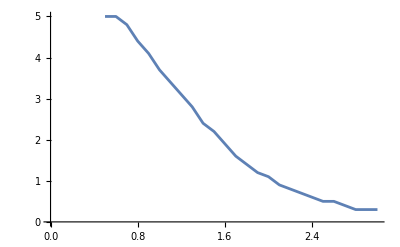
```mathematica
Show[ListPlot[table300DirectFAll, Joined->True], -Graphics-]
```

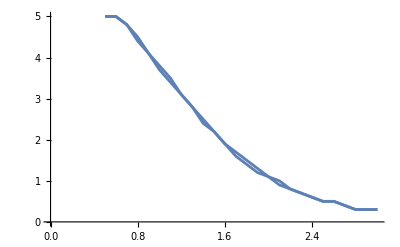

### Plotting all the results

```mathematica
listk1 = Range[0.5, 3, 0.1];
getAux["table300DirectZM.mx"];
getAux["table300Direct.mx"];
getAux["table300DirectF.mx"];
getAux["table300DirectFAll.mx"];
```

```mathematica
dataKxM95 = {listk1[[#]], Quantile[table300Direct[[All, # , 2]], 0.95]} & /@ (Range @ Length @ listk1);
dataKxM50 = {listk1[[#]], Quantile[table300Direct[[All, # , 2]], 0.50]} & /@ (Range @ Length @ listk1);
dataKxM95F = {listk1[[#]], Quantile[table300DirectF[[All, # , 2]], 0.95]} & /@ (Range @ Length @ listk1);
dataKxM95ZM = {listk1[[#]], Quantile[table300DirectZM[[All, # , 2]], 0.95]} & /@ (Range @ Length @ listk1);
dataKxM50ZM = {listk1[[#]], Quantile[table300DirectZM[[All, # , 2]], 0.50]} & /@ (Range @ Length @ listk1);
(*dataKxM50F = {listk1[[#]], Quantile[table300DirectF[[All, # , 2]], 0.50]} & /@ (Range @ Length @ listk1);*)
(*M50F is not a trustworth procedure for the forecast. There is an issue with the mass distribution below 5, 
which is not relevant for M50, M95 and M95F. For each 250 random events, there is about 1 below 5.*)

kXm95I = Interpolation[dataKxM95, InterpolationOrder->2, Method->"Spline" ];
kXm50I = Interpolation[dataKxM50, InterpolationOrder->2, Method->"Spline"];
kXm95FI = Interpolation[dataKxM95F, InterpolationOrder->2, Method->"Spline" ];
kXm50ZMI = Interpolation[dataKxM50ZM, InterpolationOrder->2, Method->"Spline"];
kXm95ZMI = Interpolation[dataKxM95ZM, InterpolationOrder->2, Method->"Spline" ];
(*kXm50FI = Interpolation[dataKxM50F, InterpolationOrder->2, Method->"Spline"];*)
kXmFAllI = Interpolation[table300DirectFAll, InterpolationOrder->2, Method->"Spline"];
(*kXmFAllI is between kXm95FI and kXm50FI*)
```

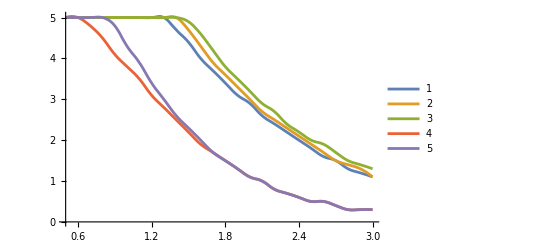

```mathematica
Plot[{kXm50ZMI[k], kXm95ZMI[k], kXm95I[k], kXmFAllI[k], kXm95FI[k]}, {k,0.5, 3}, PlotLegends->Automatic]
```

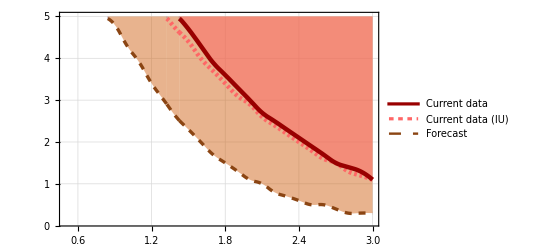

pathOut/plotkXmDirect.pdf

```mathematica
color1i = RGBColor[0, 76/255, 153/255];
color1ii = RGBColor[51/255, 153/255, 255/255];
color1iii = RGBColor[153/255, 0, 0];
color1iv = RGBColor[255/255, 102/255, 102/255];
color2i = RGBColor[128/255, 0, 128/255];
color2ii = RGBColor[191/255, 85/255, 236/255];
color2iii = RGBColor[255/255, 140/255, 0];
color2iv = RGBColor[255/255, 179/255, 71/255];
color3i = RGBColor[0, 128/255, 128/255];
color3ii = RGBColor[0, 192/255, 192/255];
color3iii = RGBColor[139/255, 69/255, 19/255];
color3iv = RGBColor[210/255, 105/255, 30/255];

legend = LineLegend[
  {
    Directive[Thickness[0.008], color1iii],
    Directive[Thickness[0.008], color1iv, Dashing[0.005]], 
    Directive[Thickness[0.006], color3iii, Dashed]
  },
  {
    Style["Current data", FontFamily->"Times", FontSize -> 14], 
    Style["Current data (IU)", FontFamily->"Times", FontSize -> 14],
    Style["Forecast", FontFamily->"Times", FontSize -> 14]
  },    
  LegendMarkerSize->{25, 5}
];

plotkXmDirect = Plot[
  {
    200 (*If[kXmFAllI[k]>=4.95, 200, kXmFAllI[k]]*),
    If[kXm95FI[k]>=4.95, 200, kXm95FI[k]], 
    If[kXm50ZMI[k]>=4.95, 200, kXm50ZMI[k]],
    If[kXm95ZMI[k]>=4.95, 200,kXm95ZMI[k]] 
  }, 
  {k,0.5, 3}, 
  PlotRange->{{0.5, 3}, {0.09,5}},
  PlotStyle -> {
    {Thickness[0.006], color3iv},
    {Thickness[0.006], color3iii, Dashed},
    {Thickness[0.008], color1iv, Dashing[0.005]},
    {Thickness[0.008], color1iii}
  },
  Background -> White,
  Frame -> True,
  Axes -> False,
  Filling->{2-> {Top, Directive[Opacity[0.5], color3iv]}, 1-> None, 4-> {Top, Directive[Opacity[0.5], color1iv]}, 3-> None},
  FrameStyle-> Directive[Black, FontSize -> 13, FontFamily-> "Times"],
  FrameTicksStyle -> Directive[Black],
  GridLines->(*{{1.65, 2.1}, {}}*)Automatic,
  MaxRecursion->15,
  Epilog-> Inset[legend, Scaled[{0.22, 0.20}]]
]

exportOut["plotkXmDirect.pdf", plotkXmDirect]
```

## Exclusion plot k x MinMass using the central values (Direct method): a test

### First step: using the central mass value

```mathematica
(*
  Setting the functions zTime and timeZ:
  ---------------------------------------
*)

getAux["tablezTime.mx"]
(*zTime[t_?NumberQ] := zTime[t, -1];*)
(*table`zTime = ParallelTable[
    {t, zTime[t]}, 
    {t, 0.0005 (*z ~ 1000*), 15, 0.0005}
  ]; // EchoTiming  (*413 seconds*) 
*)
(*dumpsave["tablezTime.mx", table`zTime]*)

table`timeZ = {#2, #1} & @@@ table`zTime; (*It will be used to define the inverse function.*)
zTimeI = Interpolation[table`zTime];
timeZI = Interpolation[table`timeZ];

(*
  The observational central data:
  -------------------------------
*)

dataZMCentral = mXzDataForPlotting1 /. Around[x_, y_] -> x
```

{{0.09,35.6},{0.21,23.2},{0.09,13.7},{0.2,30.8},{0.07,11.},{0.49,50.2},{0.2,35.},{0.12,30.6},{0.21,35.4},{0.35,39.5},{0.29,24.8},{0.15,27.7},{0.62,51.3},{0.45,42.},{0.29,41.3},{0.28,23.2},{0.4,36.},{0.33,39.2},{0.45,65.1},{0.56,98.4},{0.21,43.4},{0.44,35.6},{0.49,71.8},{0.5,58.},{0.18,35.1},{0.38,54.1},{0.6,74.},{0.17,12.1},{0.19,19.8},{0.16,14.2},{0.52,38.9},{0.18,12.5},{0.54,37.7},{0.05,23.3},{0.38,31.9},{0.29,23.7},{0.29,43.8},{0.32,32.6},{0.11,8.8},{0.19,20.8},{0.53,66.3},{0.16,14.2},{0.23,10.7},{0.25,65.},{0.57,53.},{0.16,10.7},{0.13,11.9},{0.35,24.9},{0.07,12.1},{0.51,45.1},{0.69,49.4},{0.24,35.6},{0.06,5.9},{0.56,42.2},{0.18,34.5},{0.09,10.1},{0.4,37.8},{0.57,35.6},{0.57,37.5},{0.32,40.},{0.22,19.3},{0.28,37.8},{0.23,34.2},{0.22,13.1},{0.56,33.7},{0.61,36.6},{0.2,11.8},{0.56,41.8},{0.92,46.2},{0.15,9.7},{0.2,11.8},{0.63,51.}}

```mathematica
Clear[
  massFactor1, 
  massFactorDelay1, 
  dataMassFactor1, 
  dataM1ObsFormation
];

dataDelayTime[zm_] := dataDelayTime[zm] = dataDelayTime[zm, tdmin0, tdmax0, zMax0, w0];
massFactor1[zm_,zi_] = (1 + zi)/(1 + zm); (*This is the massFactor for k = 1*)

SetAttributes[massFactorDelay1, Listable];
massFactorDelay1[zm_, td_] =  massFactor1[zm, zTimeI[timeZI[zm] - td]];
dataMassFactor1[zm_] := dataMassFactor1[zm] = massFactorDelay1[zm, dataDelayTime[zm]];
dataM1ObsFormation[k_] :=  dataM1ObsFormation[k] = (#2 / dataMassFactor1[#1]^k) &  @@@ dataZMCentral;
```

```mathematica
dataM1ObsFormation[3]; //EchoTiming
```

138.245

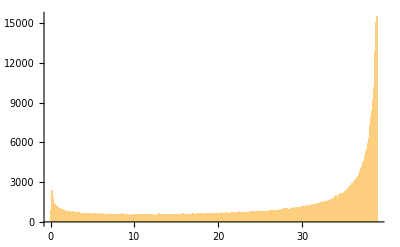

```mathematica
Histogram[dataM1ObsFormation[3][[10]], {0.1}, PlotRange->All]
```

```mathematica
Clear[𝒟M1ObsFormation];
𝒟M1ObsFormation[k_, event_] := 𝒟M1ObsFormation[k, event] = EmpiricalDistribution[dataM1ObsFormation[k][[event]]];
```

316.502

```mathematica
Clear[probabiltyNoBHwithMassBelow];
probabiltyNoBHwithMassBelow[k_, minM_] := Product[SurvivalFunction[𝒟M1ObsFormation[k, event], minM], {event, 1, 72}];
```

```mathematica
probabiltyNoBHwithMassBelow[3, 2] // sigmaProb
```

2.64013

```mathematica
Clear[tab, sol, solAll, probValue];
probValue = probSigma[2];
listk1 = Range[0.5, 3, 0.1];
listm1 = Range[0.4, 5, 0.1];
sol[0] = {arbitraryK, Last @ listm1}; (*Only used for the first step.*)

tab[nk1_] := tab[nk1] = Block[{nm1Previous, nm1Minimal, listm1Relevant},
  nm1Previous = Position[listm1, Last @ sol[nk1-1]][[1,1]];
  nm1Minimal = If[nm1Previous - 10 < 1, 1, nm1Previous - 10];
  listm1Relevant = listm1 // Take[#, {nm1Minimal, nm1Previous}] &;
  Table[
    {{listk1[[nk1]], m1}, Abs[probabiltyNoBHwithMassBelow[listk1[[nk1]], m1] - probValue]} , 
    {m1, listm1Relevant}
  ]
];
sol[nk1_] := sol[nk1] = tab[nk1] // SortBy[#, Last][[1,1]] & (*// Echo*);

solAll := solAll = Monitor[Table[sol[nk1], {nk1, Length @ listk1}], nk1];
```

```mathematica
listk1 // Length
```

26

```mathematica
sol[26]
```

{3.,1.1}

```mathematica
solAll // EchoTiming
```

0.064596

{{0.5,5.},{0.6,5.},{0.7,5.},{0.8,5.},{0.9,5.},{1.,5.},{1.1,5.},{1.2,5.},{1.3,5.},{1.4,4.8},{1.5,4.4},{1.6,4.1},{1.7,3.8},{1.8,3.4},{1.9,3.1},{2.,2.9},{2.1,2.6},{2.2,2.4},{2.3,2.2},{2.4,2.},{2.5,1.8},{2.6,1.6},{2.7,1.5},{2.8,1.3},{2.9,1.2},{3.,1.1}}

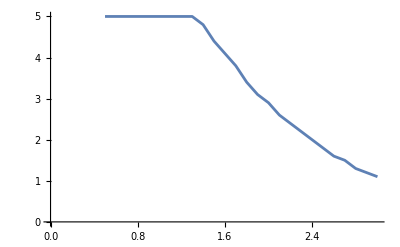

```mathematica
ListPlot[solAll, Joined->True]
```

## Checking sumit data

```mathematica
allMassesSumit = Median[posteriorM1[#]] & /@ Range @ 72 // Sort
```

{{5.84037527439188819,0.0620388399072119429},{8.90810940025874398,0.117080618988939247},{9.81892036308497307,0.149874963317912835},{10.2202397999438759,0.0885812236987924967},{10.8484551180107891,0.226705317203519621},{10.979042742187195,0.0692597257038780403},{10.9873772044097215,0.158621647723132156},{11.5894600169528603,0.157578976745505264},{11.9952632209399503,0.197532001521164152},{12.0351093784113328,0.216968609894121492},{12.2248451651196755,0.155968326546413585},{12.2398098679087637,0.130650904486772398},{12.2782245033576247,0.17456103562161647},{12.6874965261325618,0.0729367963935333014},{13.3465885999641474,0.158721668541315045},{13.8310318604699294,0.0942780522216900077},{14.2459809365644618,0.213821354246868586},{17.4970695058828465,0.176350476797961328},{19.3951532024256625,0.214418237011980942},{21.1972540318609788,0.190004529814437453},{23.1925630791223458,0.27360753165835619},{23.1932328431243224,0.0525296824107791688},{23.229656129525619,0.212361829689708639},{24.0680273743897359,0.297708388243401928},{24.6568978159706056,0.290281056424342959},{24.7877826148586404,0.352118157514640151},{30.0634796554554296,0.149857472988109849},{30.6666384806209944,0.123590781256376542},{30.715615498806379,0.197259642508514854},{32.1156104374914229,0.385470693182484669},{34.4760940583045752,0.229157853998029334},{34.7098022429562327,0.583557623395699665},{34.8934743391818003,0.178009686927718611},{35.1239454222033167,0.20369810425211872},{35.2048727807930284,0.572157794536257869},{35.2715390481408235,0.303765131737659622},{35.3764491627913493,0.208394728083201752},{35.6879144047342791,0.0924497361665508263},{35.7775652812733647,0.373133081038790421},{35.9886347951246393,0.240393011739590018},{36.5476633351191325,0.644576705587520504},{36.7522514217938365,0.439990747431327128},{37.1324902406404824,0.190229067227081425},{37.2404130016643755,0.548692669956115153},{37.3561532663111997,0.348380153188407926},{37.4250097137196853,0.561264861972806062},{37.9570178633647721,0.393661231424823926},{38.009260752602362,0.552770943464680142},{38.5788469496489661,0.271006183025458064},{39.5200646459292138,0.353560431229549194},{40.405615490171602,0.315016909428264325},{41.3711612643153188,0.497109958325090723},{41.4525956474856514,0.549534194445464141},{41.7893889701602497,0.543082815140602193},{42.1674008002361767,0.239662275123867979},{43.0644284254279093,1.04847461974575207},{43.294654103352201,0.27462202514549211},{43.9205585717532578,0.276067217702571588},{45.5192886694415826,0.484642134930000051},{47.4834904237623086,0.712323134594274821},{48.9647382874382409,0.689773143779383369},{50.2964861408388622,0.487557962446908216},{51.6664500977395278,0.632031232762202244},{54.1508754284894884,0.369493616914491452},{57.350620113394001,0.482873825436688026},{60.8135106446092308,0.565451285685443672},{65.6339998183405129,0.219201434166280726},{66.077662262899544,0.443777806269870123},{66.8387993447761204,0.706265254089253336},{68.9687615669609855,0.466770730579425724},{81.0516697204344752,0.378350529521835788},{94.8582702072856208,0.644478954506331858}}

```mathematica
N[allMassesSumit, 3]
Reverse /@ dataZMCentral // Sort
```

{{5.84,0.062},{8.91,0.117},{9.82,0.15},{10.2,0.0886},{10.8,0.227},{11.,0.0693},{11.,0.159},{11.6,0.158},{12.,0.198},{12.,0.217},{12.2,0.156},{12.2,0.131},{12.3,0.175},{12.7,0.0729},{13.3,0.159},{13.8,0.0943},{14.2,0.214},{17.5,0.176},{19.4,0.214},{21.2,0.19},{23.2,0.274},{23.2,0.0525},{23.2,0.212},{24.1,0.298},{24.7,0.29},{24.8,0.352},{30.1,0.15},{30.7,0.124},{30.7,0.197},{32.1,0.385},{34.5,0.229},{34.7,0.584},{34.9,0.178},{35.1,0.204},{35.2,0.572},{35.3,0.304},{35.4,0.208},{35.7,0.0924},{35.8,0.373},{36.,0.24},{36.5,0.645},{36.8,0.44},{37.1,0.19},{37.2,0.549},{37.4,0.348},{37.4,0.561},{38.,0.394},{38.,0.553},{38.6,0.271},{39.5,0.354},{40.4,0.315},{41.4,0.497},{41.5,0.55},{41.8,0.543},{42.2,0.24},{43.1,1.05},{43.3,0.275},{43.9,0.276},{45.5,0.485},{47.5,0.712},{49.,0.69},{50.3,0.488},{51.7,0.632},{54.2,0.369},{57.4,0.483},{60.8,0.565},{65.6,0.219},{66.1,0.444},{66.8,0.706},{69.,0.467},{81.1,0.378},{94.9,0.644}}

{{5.9,0.06},{8.8,0.11},{9.7,0.15},{10.1,0.09},{10.7,0.16},{10.7,0.23},{11.,0.07},{11.8,0.2},{11.8,0.2},{11.9,0.13},{12.1,0.07},{12.1,0.17},{12.5,0.18},{13.1,0.22},{13.7,0.09},{14.2,0.16},{14.2,0.16},{19.3,0.22},{19.8,0.19},{20.8,0.19},{23.2,0.21},{23.2,0.28},{23.3,0.05},{23.7,0.29},{24.8,0.29},{24.9,0.35},{27.7,0.15},{30.6,0.12},{30.8,0.2},{31.9,0.38},{32.6,0.32},{33.7,0.56},{34.2,0.23},{34.5,0.18},{35.,0.2},{35.1,0.18},{35.4,0.21},{35.6,0.09},{35.6,0.24},{35.6,0.44},{35.6,0.57},{36.,0.4},{36.6,0.61},{37.5,0.57},{37.7,0.54},{37.8,0.28},{37.8,0.4},{38.9,0.52},{39.2,0.33},{39.5,0.35},{40.,0.32},{41.3,0.29},{41.8,0.56},{42.,0.45},{42.2,0.56},{43.4,0.21},{43.8,0.29},{45.1,0.51},{46.2,0.92},{49.4,0.69},{50.2,0.49},{51.,0.63},{51.3,0.62},{53.,0.57},{54.1,0.38},{58.,0.5},{65.,0.25},{65.1,0.45},{66.3,0.53},{71.8,0.49},{74.,0.6},{98.4,0.56}}

```mathematica
Reverse /@ N[allMassesSumit, 3] // Sort // Export["sumitMedian.csv", #] &
dataZMCentral // Sort // Export["LVKvalues.csv", #] &
```

sumitMedian.csv

LVKvalues.csv

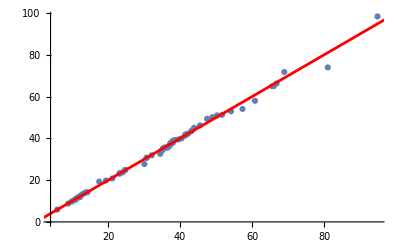

```mathematica
Show[ListPlot[{allMassesSumit[[All,1]] // Sort, dataZMCentral[[All,2]]// Sort}ᵀ, PlotRange->All], Plot[x, {x,0,100}, PlotStyle->Red], Background->White]
```

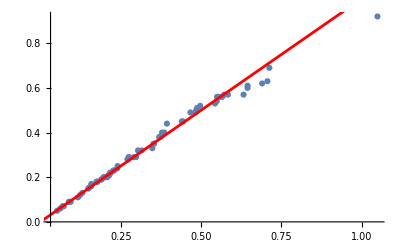

```mathematica
Show[ListPlot[{allMassesSumit[[All,2]] // Sort, dataZMCentral[[All,1]]// Sort}ᵀ, PlotRange->All], Plot[x, {x,0,100}, PlotStyle->Red], Background->White]
```

```mathematica
allMassesSumit // Length
```

72

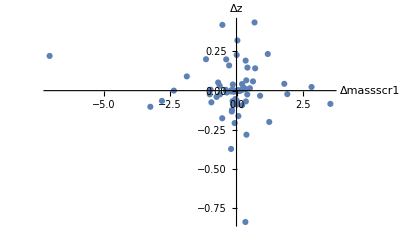

```mathematica
(Reverse /@ dataZMCentral // Sort) - (allMassesSumit // Sort) // ListPlot[#, 
  Background->White,
  AxesLabel->{"Δmassscr1", "Δz"}, PlotRange->All]&
```

```mathematica
Import[eventsFileNames[[1]], "Table"]
```

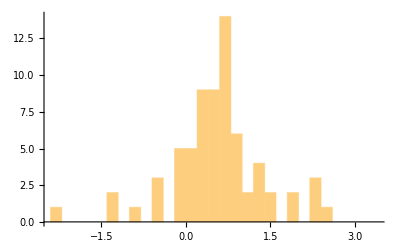

```mathematica
((allMassesSumit // Sort) - allMasses) // Histogram[#, {0.2}] &
```

```mathematica
posteriorM1[1] // Median
```

35.6879144047342791

```mathematica
Median[posteriorM1[1]]
```

Median::rectt: Rectangular array expected at position 1 in Median[35.6879144047342791].

Median[35.6879144047342791]

```mathematica
allMasses = dataZMCentral[[All, 2]] // Sort
```

{5.9,8.8,9.7,10.1,10.7,10.7,11.,11.8,11.8,11.9,12.1,12.1,12.5,13.1,13.7,14.2,14.2,19.3,19.8,20.8,23.2,23.2,23.3,23.7,24.8,24.9,27.7,30.6,30.8,31.9,32.6,33.7,34.2,34.5,35.,35.1,35.4,35.6,35.6,35.6,35.6,36.,36.6,37.5,37.7,37.8,37.8,38.9,39.2,39.5,40.,41.3,41.8,42.,42.2,43.4,43.8,45.1,46.2,49.4,50.2,51.,51.3,53.,54.1,58.,65.,65.1,66.3,71.8,74.,98.4}

```mathematica
dataZMCentral // Sort
```

{{0.05,23.3},{0.06,5.9},{0.07,11.},{0.07,12.1},{0.09,10.1},{0.09,13.7},{0.09,35.6},{0.11,8.8},{0.12,30.6},{0.13,11.9},{0.15,9.7},{0.15,27.7},{0.16,10.7},{0.16,14.2},{0.16,14.2},{0.17,12.1},{0.18,12.5},{0.18,34.5},{0.18,35.1},{0.19,19.8},{0.19,20.8},{0.2,11.8},{0.2,11.8},{0.2,30.8},{0.2,35.},{0.21,23.2},{0.21,35.4},{0.21,43.4},{0.22,13.1},{0.22,19.3},{0.23,10.7},{0.23,34.2},{0.24,35.6},{0.25,65.},{0.28,23.2},{0.28,37.8},{0.29,23.7},{0.29,24.8},{0.29,41.3},{0.29,43.8},{0.32,32.6},{0.32,40.},{0.33,39.2},{0.35,24.9},{0.35,39.5},{0.38,31.9},{0.38,54.1},{0.4,36.},{0.4,37.8},{0.44,35.6},{0.45,42.},{0.45,65.1},{0.49,50.2},{0.49,71.8},{0.5,58.},{0.51,45.1},{0.52,38.9},{0.53,66.3},{0.54,37.7},{0.56,33.7},{0.56,41.8},{0.56,42.2},{0.56,98.4},{0.57,35.6},{0.57,37.5},{0.57,53.},{0.6,74.},{0.61,36.6},{0.62,51.3},{0.63,51.},{0.69,49.4},{0.92,46.2}}

```mathematica
dataZMCentral = mXzDataForPlotting1 /. Around[x_, y_] -> x
```

{{0.09,35.6},{0.21,23.2},{0.09,13.7},{0.2,30.8},{0.07,11.},{0.49,50.2},{0.2,35.},{0.12,30.6},{0.21,35.4},{0.35,39.5},{0.29,24.8},{0.15,27.7},{0.62,51.3},{0.45,42.},{0.29,41.3},{0.28,23.2},{0.4,36.},{0.33,39.2},{0.45,65.1},{0.56,98.4},{0.21,43.4},{0.44,35.6},{0.49,71.8},{0.5,58.},{0.18,35.1},{0.38,54.1},{0.6,74.},{0.17,12.1},{0.19,19.8},{0.16,14.2},{0.52,38.9},{0.18,12.5},{0.54,37.7},{0.05,23.3},{0.38,31.9},{0.29,23.7},{0.29,43.8},{0.32,32.6},{0.11,8.8},{0.19,20.8},{0.53,66.3},{0.16,14.2},{0.23,10.7},{0.25,65.},{0.57,53.},{0.16,10.7},{0.13,11.9},{0.35,24.9},{0.07,12.1},{0.51,45.1},{0.69,49.4},{0.24,35.6},{0.06,5.9},{0.56,42.2},{0.18,34.5},{0.09,10.1},{0.4,37.8},{0.57,35.6},{0.57,37.5},{0.32,40.},{0.22,19.3},{0.28,37.8},{0.23,34.2},{0.22,13.1},{0.56,33.7},{0.61,36.6},{0.2,11.8},{0.56,41.8},{0.92,46.2},{0.15,9.7},{0.2,11.8},{0.63,51.}}